## Definitions

```mathematica
<< KnotTheory`
```

Loading KnotTheory` version of November 29, 2007, 19:46:57.5156.
Read more at http://katlas.math.toronto.edu/wiki/KnotTheory.

```mathematica
BeginPackage["KnotTheory`"];

ArcPresentation; Draw; MorseLink; Cup; Cap; X; Over; Under; Reduce; PD; OverlayMatrix; Up; Down;

ArcPresentation::usage = "ArcPresentation[{a1,b1}, {a2, b2}, ..., {an,bn}] is an arc presentation of a knot (as often used in the realm of Heegaard-Floer homologies), where the horizontal arc at row i connects column ai to column bi. ArcPresentation[K] returns an arc presentation of the knot K. ArcPresentation[K, Reduce -> r] attemps at most r reduction steps (using a naive reduction algorithm) following a naive creation of some arc presentation for K.";

Draw::usage = "Draw[ap] draws the Arc Presentation ap. Draw[ap, OverlayMatrix -> M] overlays the matrix M on top of that draw.";

Begin["`ArcPresentation`"];

InterlacedQ[{a_,b_}, {c_,d_}] := (Signature[{a,b}]Signature[{c,d}]Signature[{a,b,c,d}]===-1);
Slidable[a_,b_,m_List] := Module[
{h},
Or[
!(Or @@ (InterlacedQ[{a,b}, #]& /@ m)),
SameQ[0,
Total[h /@ Select[
Sort[Flatten[m]],
(Min[a,b]<#<Max[a,b])&
]] /. 2h[_] -> 0
]
]
];
Options[ArcPresentation] = {Reduce -> Infinity};
ArcPresentation[ml_MorseLink, opts___Rule] := Module[
{
ActiveVerts, VertOrdering, vc,out,m,n,k,p,b,c,br,bl,r, l, UnneededVerts, AP, redsdone, oldreds, 
red = Reduce /. {opts} /. Options[ArcPresentation]
},
ActiveVerts={}; VertOrdering={}; vc=0;
out = (List @@ ml) /. {
Cup[m_,n_] :> (
k = Min[m,n];
ActiveVerts = Insert[ActiveVerts, ++vc, k];
ActiveVerts = Insert[ActiveVerts, ++vc, k+1];
If[k==1,
VertOrdering={vc-1, vc}~Join~VertOrdering,
{{p}} = Position[VertOrdering, ActiveVerts[[k-1]]];
VertOrdering = Insert[VertOrdering, vc-1, p+1];
VertOrdering = Insert[VertOrdering,  vc, p+2];
];
{m,n}-k+vc-1 
),
X[n_, Under, b_, c_] :>  (
bl=ActiveVerts[[n]];
ActiveVerts = Insert[Delete[ActiveVerts,  n], ++vc, n+1];
{{p}} = Position[VertOrdering, ActiveVerts[[n]]];
VertOrdering = Insert[VertOrdering,  vc, p+1];
If[b===Up, {bl, vc}, {vc,bl}]
),
X[n_, Over, b_, c_] :>  (
br=ActiveVerts[[n+1]];
ActiveVerts = Insert[Delete[ActiveVerts,  n+1], ++vc, n];
{{p}} = Position[VertOrdering, ActiveVerts[[n+1]]];
VertOrdering = Insert[VertOrdering,  vc, p];
If[c===Up, {br, vc}, {vc,br}]
),
Cap[m_, n_] :> (
r={ActiveVerts[[m]], ActiveVerts[[n]]};
ActiveVerts = Delete[ActiveVerts, {{m}, {n}}];
r
)
} /. Thread[Rule[VertOrdering, Range[Length[VertOrdering]]]];
redsdone=0; oldreds=-1; UnneededVerts={};
While[redsdone < red && redsdone > oldreds,
oldreds=redsdone;
out = (AP @@ out) /. {
AP[l___, {a_, b_}, m___, {b_,c_}, r___] /; (a≠c && Slidable[a,b,{m}]) :> (
++redsdone; AppendTo[UnneededVerts, b];
AP[l, m, {a,c}, r]
),
AP[l___, {b_, a_}, m___, {c_,b_}, r___] /; (a≠c && Slidable[a,b,{m}]) :> (
++redsdone; AppendTo[UnneededVerts, b];
AP[l, m, {c, a}, r]
),
AP[l___, {b_, c_}, m___, {a_,b_}, r___] /; (a≠c && Slidable[a,b,{m}]) :> (
++redsdone; AppendTo[UnneededVerts, b];
AP[l,  {a,c}, m, r]
),
AP[l___, {c_, b_}, m___, {b_,a_}, r___] /; (a≠c && Slidable[a,b,{m}]) :> (
++redsdone; AppendTo[UnneededVerts, b];
AP[l,  {c, a}, m, r]
)
}
];
out = out /. Thread[Rule[Delete[Range[vc], List /@ UnneededVerts], Range[vc-Length[UnneededVerts]]]];
ArcPresentation @@ out
];
ArcPresentation[K_, opts___Rule] := ArcPresentation[MorseLink[K], opts];

Options[Draw] = {OverlayMatrix -> Null};
Draw[ap_ArcPresentation, opts___Rule]  := Module[
{
l,p1,p2,k, V,
om = OverlayMatrix /. {opts} /. Options[Draw]
},
l = Length[ap];
Graphics[Flatten[{
{Thickness[1/10/Length[ap]]},
Table[
Line[{{ap[[k, 1]], k}, {ap[[k,2]], k}}],
{k,l}
],
{Thickness[0.45/Length[ap]], GrayLevel[1]},
Table[
{{p1}} = Position[First /@ ap, k];
{{p2}} = Position[Last /@ ap, k];
{p1, p2} = Sort[{p1,p2}];
Line[{{k, p1+0.5}, {k, p2-0.5}}],
{k, l}
],
{Thickness[1/10/Length[ap]], GrayLevel[0]},
Table[
{{p1}} = Position[First /@ ap, k];
{{p2}} = Position[Last /@ ap, k];
Line[{{k, p1}, {k, p2}}],
{k, l}
],
If[om===Null, {},
MapIndexed[
Text[#1, 0.5+#2]&,
Transpose[om], {2}
]
]
}]]
]

SwapAt[l_List, j_Integer] := Join[
Take[l, j-1], l[[{j+1, j}]], Drop[l, j+1]
];
ArcPresentation /: MorseLink[ap_ArcPresentation] := Module[
{
ml={}, (* holds the MorseLink under construction *)
strands={}, (* the ArcPresentation numbering of the active strands *)
dirs = {}, (* the orientations of the active strands *)
k, cur, fr, to, type, frind, toind, start, end, j
},
AddXings[start_, end_] := If[end>start,
Do[
AppendTo[ml, X[j, Under, dirs[[j]], dirs[[j+1]]]];
strands=SwapAt[strands, j];
dirs = SwapAt[dirs, j],
{j, start, end-1}
],
Do[
AppendTo[ml, X[j-1, Over, dirs[[j-1]], dirs[[j]]]];
strands=SwapAt[strands, j-1];
dirs = SwapAt[dirs, j-1],
{j, start, end+1, -1}
]
];
Do[
{
{fr, to} = cur = ap[[k]],
{frind, toind} = (1+Count[strands, i_ /; i<#])& /@ cur,
type = {MemberQ[strands, #]& /@ cur, Sign[to-fr]}
};
Switch[type,
{{False, False}, +1}, (
AppendTo[ml, Cup[frind, frind+1]];
strands = Flatten[Insert[strands, {fr, to}, frind]];
dirs = Flatten[Insert[dirs, {Down, Up}, frind]];
AddXings[frind+1, toind+1]
),
{{False, True}, +1}, (
strands[[toind]] = fr;
AddXings[toind, frind]
),
{{True, False}, +1}, (
strands[[frind]]=to;
AddXings[frind, toind-1]
),
{{True, True}, +1}, (
AddXings[frind, toind-1];
AppendTo[ml, Cap[toind-1, toind]];
strands = Delete[strands, {{toind-1}, {toind}}];
dirs = Delete[dirs, {{toind-1}, {toind}}]
),
{{False, False}, -1}, (
AppendTo[ml, Cup[frind+1, frind]];
strands = Flatten[Insert[strands, {to, fr}, frind]];
dirs = Flatten[Insert[dirs, {Up, Down}, frind]];
AddXings[frind, toind]
),
{{False, True}, -1}, (
strands[[toind]]=fr;
AddXings[toind, frind-1]
),
{{True, False}, -1},(
strands[[frind]]=to;
AddXings[frind, toind]
),
{{True, True}, -1}, (
AddXings[frind, toind+1];
AppendTo[ml, Cap[toind+1, toind]];
strands = Delete[strands, {{toind+1}, {toind}}];
dirs = Delete[dirs, {{toind+1}, {toind}}]
)
],
{k,Length[ap]}
];
MorseLink @@ ml
];
PD[ap_ArcPresentation] := (ml=MorseLink[ap]; PD[ml]);

End[]; EndPackage[];
```

## Presentation

```mathematica
?ArcPresentation
```

ArcPresentation[{a1,b1}, {a2, b2}, ..., {an,bn}] is an arc presentation of a knot (as often used in the realm of Heegaard-Floer homologies), where ai is horizontal arc at row i connects column ai to column bi. ArcPresentation[K] returns an arc presentation of the knot K. ArcPresentation[K, Reduce -> r] attemps at most r reduction steps (using a naive reduction algorithm) following a naive creation of some arc presentation for K.

```mathematica
ap=ArcPresentation["K11n11"]
```

KnotTheory::loading: Loading precomputed data in "DTCode4KnotsTo11`".

KnotTheory::credits: "The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005."

KnotTheory::credits: "MorseLink was added to KnotTheory` by Siddarth Sankaran\nat the University of Toronto in the summer of 2005."

ArcPresentation[{12,2},{1,10},{3,9},{5,11},{9,12},{4,8},{2,5},{11,7},{8,6},{7,4},{10,3},{6,1}]

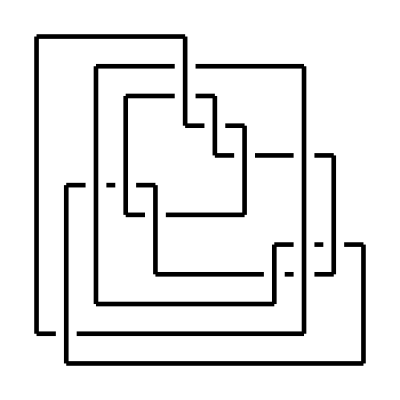

```mathematica
Draw[ap]
```

```mathematica
ap0=ArcPresentation["K11n11", Reduce -> 0]
```

ArcPresentation[{13,19},{20,23},{19,22},{15,14},{14,2},{1,13},{3,12},{2,4},{16,18},{17,15},{8,16},{12,17},{5,7},{4,6},{7,11},{6,8},{18,10},{11,9},{10,21},{9,20},{21,5},{22,3},{23,1}]

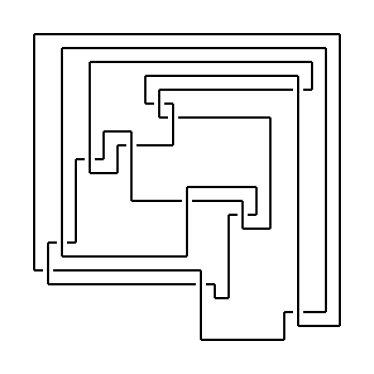

```mathematica
Draw[ap0]
```

```mathematica
br=BR[ap]
```

KnotTheory::credits: "Vogel's algorithm was implemented by Dan Carney in the summer of 2005 at the University of Toronto."

BR[4,{-1,2,3,3,-2,-1,-2,-1,2,3,3,3,2}]

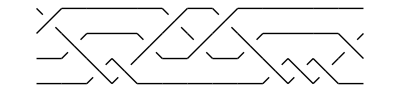

```mathematica
BraidPlot[br]
```

```mathematica
Reflect[ap_ArcPresentation] := ArcPresentation @@ (
(Last /@ Sort[Reverse /@ Position[ap, #]])& /@ Range[Length[ap]]
)
```

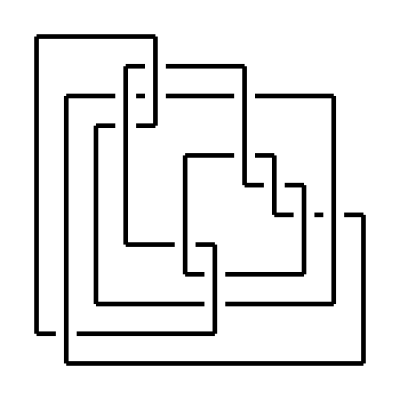

```mathematica
Reflect[ap] // Draw
```

```mathematica
MinesweeperMatrix[ap_ArcPresentation] := Module[
{l, CurrentRow, c1,c2,k,s},
l=Length[ap];
CurrentRow = Table[0, {l}];
Table[
{c1, c2} = Sort[ap[[k]]];
s=Sign[{-1,1}.ap[[k]]];
Do[
CurrentRow[[c]]+=s,
{c, c1, c2-1}
];
CurrentRow,
{k,l}
]
];
```

```mathematica
?Draw
```

Draw[ap] draws the Arc Presentation ap. Draw[ap, OverlayMatrix -> M] overlays the matrix M on top of that draw.

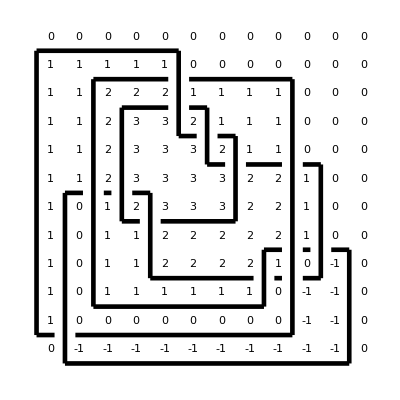

```mathematica
Draw[ap, OverlayMatrix ->MinesweeperMatrix[ap]]
```

```mathematica
{Det[t^MinesweeperMatrix[ap]], Alexander[ap][t]} // Factor
```

{(-1+t)^11 t^2 (1-5 t+13 t^2-17 t^3+13 t^4-5 t^5+t^6),(1-5 t+13 t^2-17 t^3+13 t^4-5 t^5+t^6)/t^3}

## Further Testing

```mathematica
Test[K_] := (K -> Jones[K][q] == Jones[ArcPresentation[K]][q])
```

```mathematica
test= Test /@ AllKnots[10]
```

KnotTheory::loading: Loading precomputed data in "Jones4Knots`".

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

{Knot[10,1]→True,Knot[10,2]→True,Knot[10,3]→True,Knot[10,4]→True,Knot[10,5]→True,Knot[10,6]→True,Knot[10,7]→True,Knot[10,8]→True,Knot[10,9]→True,Knot[10,10]→True,Knot[10,11]→True,Knot[10,12]→True,Knot[10,13]→True,Knot[10,14]→True,Knot[10,15]→True,Knot[10,16]→True,Knot[10,17]→True,Knot[10,18]→True,Knot[10,19]→True,Knot[10,20]→True,Knot[10,21]→True,Knot[10,22]→True,Knot[10,23]→True,Knot[10,24]→True,Knot[10,25]→True,Knot[10,26]→True,Knot[10,27]→True,Knot[10,28]→True,Knot[10,29]→True,Knot[10,30]→True,Knot[10,31]→True,Knot[10,32]→True,Knot[10,33]→True,Knot[10,34]→True,Knot[10,35]→True,Knot[10,36]→True,Knot[10,37]→True,Knot[10,38]→True,Knot[10,39]→True,Knot[10,40]→True,Knot[10,41]→True,Knot[10,42]→True,Knot[10,43]→True,Knot[10,44]→True,Knot[10,45]→True,Knot[10,46]→True,Knot[10,47]→True,Knot[10,48]→True,Knot[10,49]→True,Knot[10,50]→True,Knot[10,51]→True,Knot[10,52]→True,Knot[10,53]→True,Knot[10,54]→True,Knot[10,55]→True,Knot[10,56]→True,Knot[10,57]→True,Knot[10,58]→True,Knot[10,59]→True,Knot[10,60]→True,Knot[10,61]→True,Knot[10,62]→True,Knot[10,63]→True,Knot[10,64]→True,Knot[10,65]→True,Knot[10,66]→True,Knot[10,67]→True,Knot[10,68]→True,Knot[10,69]→True,Knot[10,70]→True,Knot[10,71]→True,Knot[10,72]→True,Knot[10,73]→True,Knot[10,74]→True,Knot[10,75]→True,Knot[10,76]→True,Knot[10,77]→True,Knot[10,78]→True,Knot[10,79]→True,Knot[10,80]→True,Knot[10,81]→True,Knot[10,82]→True,Knot[10,83]→True,Knot[10,84]→True,Knot[10,85]→True,Knot[10,86]→True,Knot[10,87]→True,Knot[10,88]→True,Knot[10,89]→True,Knot[10,90]→True,Knot[10,91]→True,Knot[10,92]→True,Knot[10,93]→True,Knot[10,94]→True,Knot[10,95]→True,Knot[10,96]→True,Knot[10,97]→True,Knot[10,98]→True,Knot[10,99]→True,Knot[10,100]→True,Knot[10,101]→True,Knot[10,102]→True,Knot[10,103]→True,Knot[10,104]→True,Knot[10,105]→True,Knot[10,106]→True,Knot[10,107]→True,Knot[10,108]→True,Knot[10,109]→True,Knot[10,110]→True,Knot[10,111]→True,Knot[10,112]→True,Knot[10,113]→True,Knot[10,114]→True,Knot[10,115]→True,Knot[10,116]→True,Knot[10,117]→True,Knot[10,118]→True,Knot[10,119]→True,Knot[10,120]→True,Knot[10,121]→True,Knot[10,122]→True,Knot[10,123]→True,Knot[10,124]→True,Knot[10,125]→True,Knot[10,126]→True,Knot[10,127]→True,Knot[10,128]→True,Knot[10,129]→True,Knot[10,130]→True,Knot[10,131]→True,Knot[10,132]→True,Knot[10,133]→True,Knot[10,134]→True,Knot[10,135]→True,Knot[10,136]→True,Knot[10,137]→True,Knot[10,138]→True,Knot[10,139]→True,Knot[10,140]→True,Knot[10,141]→True,Knot[10,142]→True,Knot[10,143]→True,Knot[10,144]→True,Knot[10,145]→True,Knot[10,146]→True,Knot[10,147]→True,Knot[10,148]→True,Knot[10,149]→True,Knot[10,150]→True,Knot[10,151]→True,Knot[10,152]→True,Knot[10,153]→True,Knot[10,154]→True,Knot[10,155]→True,Knot[10,156]→True,Knot[10,157]→True,Knot[10,158]→True,Knot[10,159]→True,Knot[10,160]→True,Knot[10,161]→True,Knot[10,162]→True,Knot[10,163]→True,Knot[10,164]→True,Knot[10,165]→True}

```mathematica
Total[Last /@ test]
```

165 True